Numerical integration of the proportion of coexistence states in the first simplified model: fixing preferences

Pablo Rosillo Rodes, 2022
Final Master Thesis

```mathematica
X[s1_,s2_,α_] = (1+s2 (-2+α)-α+s1 (-1+2 s2+α))/((-1+2 s1) (-1+2 s2));
```

```mathematica
ω[s1_,s2_,α_] = ((1-s2+s1 (-3+4 s2)) (1+s2 (-2+α)-α+s1 (-1+2 s2+α)))/((-1+2 s1) (-1+s1+s2) (-1+2 s2));
λ1[s1_,s2_,α_,X_,ω_] = 1/2 (s1-2 s2-3 s1 X+3 s2 X-α+s1 α+s2 α+ω-s1 ω-s2 ω-1/2 √(4 (α-ω+s2 (2-3 X-α+ω)+s1 (-1+3 X-α+ω))^2+8 (2-5 X+4 X^2-2 α+2 X α+s1 (-2+4 s2 (1-2 X)^2+7 X-8 X^2+2 α-2 X α-ω)+ω-s2 (4-11 X+8 X^2-2 α+2 X α+ω))));
λ2[s1_,s2_,α_,X_,ω_] = 1/2 (s1-2 s2-3 s1 X+3 s2 X-α+s1 α+s2 α+ω-s1 ω-s2 ω+1/2 √(4 (α-ω+s2 (2-3 X-α+ω)+s1 (-1+3 X-α+ω))^2+8 (2-5 X+4 X^2-2 α+2 X α+s1 (-2+4 s2 (1-2 X)^2+7 X-8 X^2+2 α-2 X α-ω)+ω-s2 (4-11 X+8 X^2-2 α+2 X α+ω))));
```

```mathematica
Proportion of states that imply coexistence of X and Y
```

```mathematica
λ1simp[s1_,s2_,α_] = λ1[s1,s2,α,X[s1,s2,α],ω[s1,s2,α]];
λ2simp[s1_,s2_,α_] = λ2[s1,s2,α,X[s1,s2,α],ω[s1,s2,α]];
FInt[s1_,s2_, α_] = HeavisideTheta[Sign[-λ1simp[s1,s2,α]] ]HeavisideTheta[Sign[-λ2simp[s1,s2,α]]];
```

```mathematica
arrx = Array[#&, 30, {0,1}];
arry = arrx; 
err = 0*arrx;
```

```mathematica
For[i = 1, i <= 30, i++,arry[[i]] = NIntegrate[FInt[s1,s2,arrx[[i]]], {s1,0.5,1},{s2,0.5,s1}, IntegrationMonitor:>((errors=Through[#1@"Error"])&)]/(0.5^3);
err[[i]] = Total@errors/(0.5^3);]
```

```mathematica
N[arrx]
N[arry]
N[err]
```

{0.,0.0344828,0.0689655,0.103448,0.137931,0.172414,0.206897,0.241379,0.275862,0.310345,0.344828,0.37931,0.413793,0.448276,0.482759,0.517241,0.551724,0.586207,0.62069,0.655172,0.689655,0.724138,0.758621,0.793103,0.827586,0.862069,0.896552,0.931034,0.965517,1.}

{0.,0.269216,0.427917,0.539549,0.618951,0.673728,0.708701,0.727303,0.732161,0.725392,0.708768,0.683819,0.651895,0.614212,0.571885,0.525949,0.477377,0.427094,0.375992,0.324931,0.274753,0.226289,0.18036,0.137788,0.0993979,0.0660242,0.0385157,0.0177411,0.00459406,0.}

{0.,1.47331×10^-7,2.58894×10^-7,2.63406×10^-7,4.0594×10^-7,3.38429×10^-7,6.84442×10^-7,4.03103×10^-7,4.3233×10^-7,9.63392×10^-8,2.33002×10^-7,1.92677×10^-7,1.77584×10^-7,1.42994×10^-7,3.92541×10^-7,5.15135×10^-7,2.85072×10^-7,1.55404×10^-7,8.22899×10^-8,4.16477×10^-8,1.71205×10^-7,6.17799×10^-8,1.9837×10^-8,5.45662×10^-9,6.56749×10^-8,1.12913×10^-8,1.16086×10^-9,4.66167×10^-11,1.87812×10^-13,1.87812×10^-13}

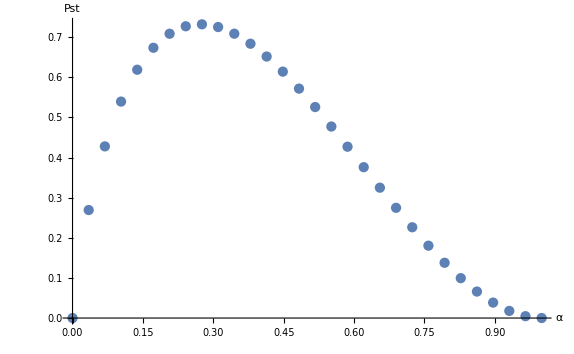

```mathematica
ListPlot[Transpose[{arrx,arry}], AxesLabel->{"α","Pst"}]
```

Error in the numerical integration:

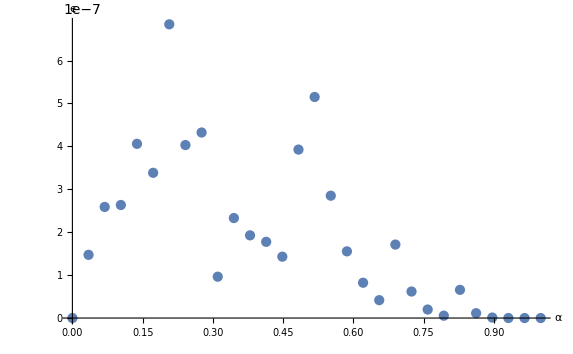

```mathematica
ListPlot[Transpose[{arrx,err}], AxesLabel->{"α","ϵ"}]
```

```mathematica
Proportion of states that imply extinction of X
```

```mathematica
λ1simp[s1_,s2_,α_] = λ1[s1,s2,α,0,0];
λ2simp[s1_,s2_,α_] = λ2[s1,s2,α,0,0];
FInt[s1_,s2_, α_] = HeavisideTheta[Sign[-λ1simp[s1,s2,α]] ]HeavisideTheta[Sign[-λ2simp[s1,s2,α]]];
```

```mathematica
arrx = Array[#&, 30, {0,1}];
arry = arrx; 
err = 0*arrx;
```

```mathematica
For[i = 1, i <= 30, i++,arry[[i]] = NIntegrate[FInt[s1,s2,arrx[[i]]], {s1,0.5,1},{s2,0.5,s1}, IntegrationMonitor:>((errors=Through[#1@"Error"])&)]/(0.5^3);
err[[i]] = Total@errors/(0.5^3);]
```

```mathematica
N[arrx]
N[arry]
N[err]
```

{0.,0.0344828,0.0689655,0.103448,0.137931,0.172414,0.206897,0.241379,0.275862,0.310345,0.344828,0.37931,0.413793,0.448276,0.482759,0.517241,0.551724,0.586207,0.62069,0.655172,0.689655,0.724138,0.758621,0.793103,0.827586,0.862069,0.896552,0.931034,0.965517,1.}

{1.,0.709152,0.527835,0.392533,0.288328,0.207529,0.145219,0.0978588,0.0627025,0.0374997,0.0203276,0.00948789,0.00343742,0.000739625,0.0000273412,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

{0.,4.77233×10^-7,4.92649×10^-7,2.6225×10^-7,9.00776×10^-8,1.7616×10^-7,1.17602×10^-7,4.22269×10^-8,1.42467×10^-8,1.92798×10^-8,3.37901×10^-9,4.28554×10^-9,2.0601×10^-9,5.14484×10^-11,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12,1.40872×10^-12}

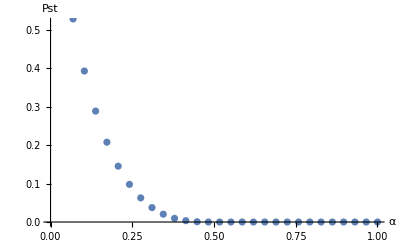

```mathematica
ListPlot[Transpose[{arrx,arry}], AxesLabel->{"α","Pst"}]
```

Error in the numerical integration:

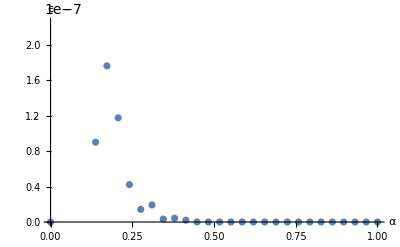

```mathematica
ListPlot[Transpose[{arrx,err}], AxesLabel->{"α","ϵ"}]
```

```mathematica
Proportion of states that imply extinction of Y
```

```mathematica
λ1simp[s1_,s2_,α_] = λ1[s1,s2,α,1,2α-1];
λ2simp[s1_,s2_,α_] = λ2[s1,s2,α,1,2α-1];
FInt[s1_,s2_, α_] = HeavisideTheta[Sign[-λ1simp[s1,s2,α]] ]HeavisideTheta[Sign[-λ2simp[s1,s2,α]]];
```

```mathematica
arrx = Array[#&, 30, {0,1}];
arry = arrx; 
err = 0*arrx;
```

```mathematica
For[i = 1, i <= 30, i++,arry[[i]] = NIntegrate[FInt[s1,s2,arrx[[i]]], {s1,0.5,1},{s2,0.5,s1}, IntegrationMonitor:>((errors=Through[#1@"Error"])&)]/(0.5^3);
err[[i]] = Total@errors/(0.5^3);]
```

```mathematica
N[arrx]
N[arry]
N[err]
```

{0.,0.0344828,0.0689655,0.103448,0.137931,0.172414,0.206897,0.241379,0.275862,0.310345,0.344828,0.37931,0.413793,0.448276,0.482759,0.517241,0.551724,0.586207,0.62069,0.655172,0.689655,0.724138,0.758621,0.793103,0.827586,0.862069,0.896552,0.931034,0.965517,1.}

{0.,0.0216321,0.0442478,0.0679181,0.092721,0.118743,0.14608,0.174838,0.205137,0.237109,0.270904,0.306693,0.344667,0.385048,0.428087,0.474051,0.522623,0.572906,0.624008,0.675069,0.725247,0.773711,0.81964,0.862212,0.900602,0.933976,0.961484,0.982259,0.995406,1.}

{1.40872×10^-12,5.72029×10^-9,1.29169×10^-8,2.19512×10^-8,3.32853×10^-8,4.7515×10^-8,6.54179×10^-8,8.80203×10^-8,1.16697×10^-7,1.53317×10^-7,2.0047×10^-7,2.61807×10^-7,3.42598×10^-7,2.10405×10^-7,3.04137×10^-7,2.5031×10^-7,2.85072×10^-7,1.55404×10^-7,8.22899×10^-8,4.33157×10^-7,1.71205×10^-7,6.17799×10^-8,1.9837×10^-8,2.76136×10^-7,6.56749×10^-8,1.12913×10^-8,1.16086×10^-9,4.66168×10^-11,1.88016×10^-13,0.}

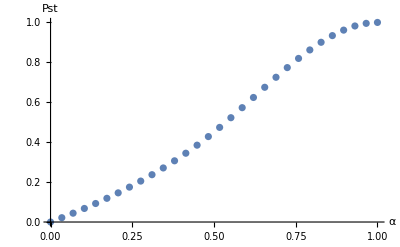

```mathematica
ListPlot[Transpose[{arrx,arry}], AxesLabel->{"α","Pst"}]
```

Error in the numerical integration:

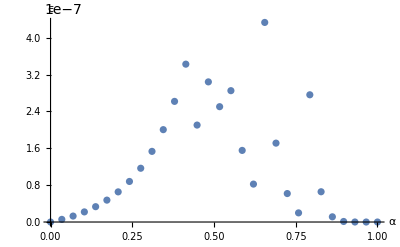

```mathematica
ListPlot[Transpose[{arrx,err}], AxesLabel->{"α","ϵ"}]
```